```mathematica
(*yellow background: import directories, file names and range of times for png output*)
```

{In-file:,E:\Uni\Masterarbeit\C++\SPR\sprdata_lengths.txt,N:,100,L:,39,lambda:,1,maxlength:,8,avg_aspect_ratio:,6,number_of_boxes:,39,rmin:,1,aimed_for_packing_fraction:,0.4,packing_fraction:,0.394477,U0:,250,F:,1,f0:,1,passive_frac:,20,passive_mode:,3,dt:,0.005,SEED,477}

100

0.0424076

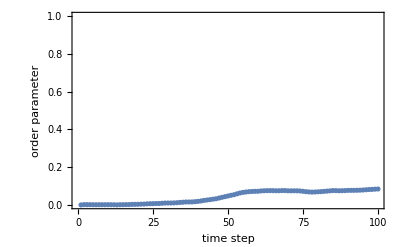

```mathematica
SetDirectory[NotebookDirectory[]]; 
$HistoryLength=5;(*no "%" etc*)

(*Import*)
output=Import["sprdata.txt","Table"];

(*read parameters from header in "output"*)
parameters=output[[1]]
l=parameters[[Position[parameters,"L:"][[1,1]]+1]];
lambda=parameters[[Position[parameters,"lambda:"][[1,1]]+1]];

(*cut out header*)
output=output[[2;;]];

(*center of mass positions as vectors {x,y}*)
points=output[[;;;;2]];
points=Map[Partition[#,2]&,points];
points=Map[Function[a,Map[{#[[1]],l-#[[2]]}&,a]],points];

(*no of timesteps*)
Length[points[[1]]]

(*angles in rad*)
angles=output[[2;;;;2]] ;

(*actual normalized velocities (vectors)*)
velocities=Map[Map[Function[angle,{Cos[angle],Sin[angle ]}],#]&,angles];

(*Order Parameter*)
Phi[list_]:=Module[{vel=1},
Norm[Total[Map[{Cos[#],Sin[#]}&,list]]]/(Length[list]*vel)
]

(*SPR: segements n by aspect ratio a*)
nBYl[a_]:=Piecewise[{{1,a==1},{3,1<a≤3},{Round[9*a/8],a>3}}]

(*import lengths and calculate number of segments n*)
lengths=Import["sprdata_lengths.txt","Table"][[1]];
ns=Map[nBYl,lengths];

(*order parameter eval*)
order=Map[Phi[#]&,angles];
Mean[order]
ListPlot[order,PlotRange->{{0,All},{0,1}},Frame->True,FrameLabel->{"time step","order parameter"}]
```

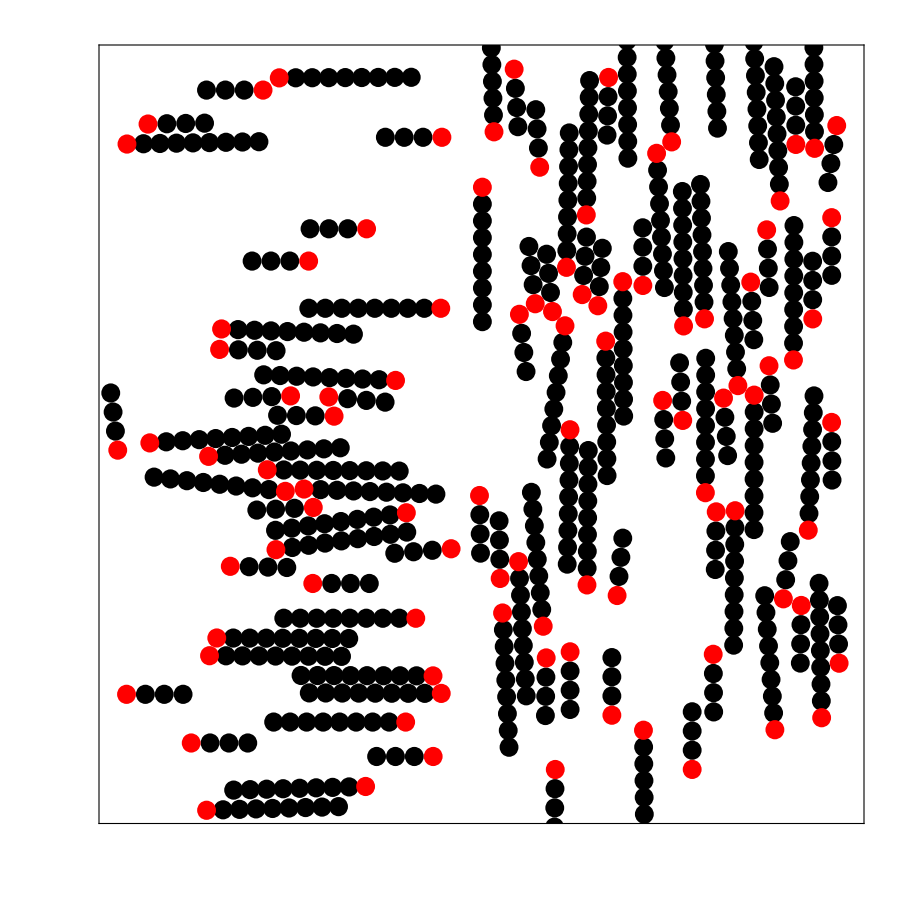

```mathematica
For[step=1,step≤10,step=step+1,

pointz=points[[step]];
velocitiez=velocities[[step]];
threadedpointsandvelocites=Thread[{pointz,velocitiez,ns,lengths}];
s=Show[
Graphics[Join[{Table[Disk[{#[[1,1]]+(-(#[[4]]-lambda)/2.+i*(#[[4]]-lambda)/(#[[3]]-1))*#[[2,1]],#[[1,2]]+(-(#[[4]]-lambda)/2.+i*(#[[4]]-lambda)/(#[[3]]-1))*#[[2,2]]},lambda/2],{i,0,#[[3]]-2,1}]},{Red,Disk[{#[[1,1]]+(-(#[[4]]-lambda)/2.+(#[[3]]-1)*(#[[4]]-lambda)/(#[[3]]-1))*#[[2,1]],#[[1,2]]+(-(#[[4]]-lambda)/2.+(#[[3]]-1)*(#[[4]]-lambda)/(#[[3]]-1))*#[[2,2]]},lambda/2]}]]&/@threadedpointsandvelocites,
Frame->True,Axes->False,FrameTicks->False,ImageSize->900,PlotRange->{{0,l},{0,l}},PlotRangeClipping->False,AspectRatio->1,ImagePadding->{{15,15},{15,15}}];
Export["spr_"<>IntegerString[step,10,9]<>".png",s];
];
s
```